```mathematica
With[
{p=5,q=7},
Monitor[
Table[
With[
{t=IntegerDigits[p^max,q]},
{CountCarries[t,p,q],Length[t]}
],
{max,0,(q-1)*q^2}
]
,{max,(q-1)*q^2}
]
]
```

{{0,1},{1,1},{2,2},{3,3},{4,4},{3,5},{4,5},{6,6},{7,7},{6,8},{7,9},{8,10},{7,10},{10,11},{9,12},{10,13},{12,14},{12,15},{12,15},{11,16},{12,17},{14,18},{16,19},{17,20},{17,20},{18,21},{18,22},{20,23},{22,24},{20,24},{18,25},{23,26},{19,27},{24,28},{21,29},{25,29},{26,30},{24,31},{26,32},{30,33},{29,34},{27,34},{26,35},{28,36},{28,37},{31,38},{31,39},{37,39},{36,40},{29,41},{36,42},{40,43},{37,44},{34,44},{38,45},{39,46},{39,47},{42,48},{38,48},{41,49},{40,50},{43,51},{45,52},{44,53},{43,53},{47,54},{48,55},{50,56},{47,57},{45,58},{48,58},{48,59},{50,60},{48,61},{51,62},{48,63},{52,63},{46,64},{53,65},{54,66},{53,67},{55,67},{58,68},{57,69},{61,70},{63,71},{59,72},{54,72},{57,73},{63,74},{62,75},{59,76},{59,77},{62,77},{63,78},{60,79},{69,80},{65,81},{63,82},{67,82},{66,83},{70,84},{70,85},{71,86},{73,87},{75,87},{69,88},{79,89},{72,90},{72,91},{74,91},{77,92},{73,93},{78,94},{76,95},{83,96},{78,96},{80,97},{83,98},{75,99},{83,100},{85,101},{82,101},{83,102},{84,103},{88,104},{86,105},{87,106},{84,106},{91,107},{87,108},{91,109},{86,110},{82,111},{97,111},{94,112},{99,113},{94,114},{88,115},{93,115},{90,116},{100,117},{104,118},{92,119},{96,120},{100,120},{100,121},{103,122},{99,123},{104,124},{93,125},{106,125},{103,126},{97,127},{104,128},{101,129},{104,130},{108,130},{110,131},{107,132},{111,133},{105,134},{110,134},{109,135},{109,136},{106,137},{109,138},{117,139},{116,139},{116,140},{116,141},{115,142},{122,143},{118,144},{117,144},{118,145},{120,146},{115,147},{116,148},{128,149},{127,149},{122,150},{128,151},{118,152},{127,153},{129,154},{129,154},{125,155},{122,156},{125,157},{126,158},{128,158},{131,159},{132,160},{142,161},{136,162},{129,163},{130,163},{134,164},{129,165},{136,166},{135,167},{138,168},{143,168},{136,169},{139,170},{140,171},{143,172},{143,173},{142,173},{138,174},{140,175},{143,176},{134,177},{137,177},{144,178},{145,179},{145,180},{147,181},{151,182},{151,182},{158,183},{146,184},{155,185},{137,186},{154,187},{155,187},{156,188},{152,189},{153,190},{163,191},{157,192},{159,192},{161,193},{157,194},{158,195},{162,196},{156,197},{161,197},{173,198},{165,199},{169,200},{160,201},{162,201},{160,202},{166,203},{168,204},{167,205},{168,206},{162,206},{157,207},{166,208},{167,209},{172,210},{175,211},{172,211},{166,212},{180,213},{178,214},{175,215},{172,216},{185,216},{184,217},{179,218},{174,219},{166,220},{177,221},{181,221},{178,222},{171,223},{170,224},{187,225},{180,225},{182,226},{181,227},{187,228},{190,229},{184,230},{173,230},{193,231},{189,232},{190,233},{194,234},{191,235},{190,235},{186,236},{203,237},{200,238},{197,239},{198,240},{191,240},{199,241},{198,242},{207,243},{208,244}}

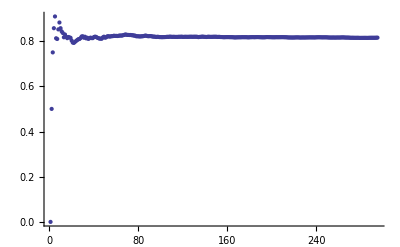

```mathematica
ListPlot[Map[#[[1]]/#[[2]]&,Accumulate[Out[218]]],PlotRange->All]
```

```mathematica
With[
{p=3,q=5},
Monitor[
Table[
With[
{t=IntegerDigits[p^max,q]},
{CountCarries[t,p,q],Length[t]}
],
{max,0,(q-1)*q^4}
]
,{max,(q-1)*q^4}
]
]
```

{{0,1},{1,1},{2,2},{1,3},{2,3},{3,4},{3,5},{5,5},{4,6},{6,7},{7,7},{6,8},{5,9},{6,9},{8,10},{9,11},{8,11},{10,12},{13,13},{11,13},{5,14},{11,15},{12,16},{10,16},{10,17},{12,18},{12,18},{15,19},{15,20},{14,20},{12,21},{17,22},{18,22},{15,23},{19,24},{17,24},{17,25},{19,26},{24,26},{19,27},{19,28},{20,28},{23,29},{22,30},{25,31},{19,31},{21,32},{25,33},{20,33},{25,34},{19,35},{29,35},{26,36},{30,37},{31,37},{27,38},{26,39},{28,39},{33,40},{35,41},{30,41},{30,42},{35,43},{29,44},{31,44},{31,45},{30,46},{34,46},{37,47},{34,48},{39,48},{36,49},{36,50},{35,50},{35,51},{36,52},{37,52},{40,53},{40,54},{37,54},{39,55},{39,56},{38,56},{42,57},{40,58},{43,59},{36,59},{41,60},{38,61},{47,61},{42,62},{43,63},{45,63},{53,64},{46,65},{46,65},{45,66},{50,67},{47,67},{51,68},{52,69},{55,69},{51,70},{43,71},{48,71},{55,72},{47,73},{57,74},{52,74},{49,75},{58,76},{60,76},{57,77},{55,78},{65,78},{60,79},{55,80},{58,80},{62,81},{58,82},{55,82},{60,83},{66,84},{60,84},{65,85},{64,86},{60,87},{60,87},{62,88},{64,89},{67,89},{73,90},{69,91},{67,91},{67,92},{63,93},{62,93},{71,94},{74,95},{71,95},{66,96},{69,97},{68,97},{73,98},{68,99},{63,99},{74,100},{79,101},{66,102},{74,102},{80,103},{80,104},{78,104},{82,105},{75,106},{70,106},{74,107},{75,108},{79,108},{79,109},{81,110},{81,110},{78,111},{80,112},{75,112},{80,113},{83,114},{88,114},{75,115},{79,116},{83,117},{90,117},{89,118},{83,119},{87,119},{79,120},{85,121},{89,121},{94,122},{92,123},{76,123},{89,124},{92,125},{94,125},{95,126},{92,127},{93,127},{98,128},{100,129},{93,130},{94,130},{94,131},{94,132},{92,132},{96,133},{95,134},{104,134},{102,135},{96,136},{98,136},{103,137},{94,138},{97,138},{102,139},{111,140},{104,140},{112,141},{114,142},{98,142},{97,143},{97,144},{109,145},{108,145},{99,146},{106,147},{108,147},{107,148},{111,149},{102,149},{98,150},{103,151},{101,151},{109,152},{106,153},{104,153},{113,154},{114,155},{107,155},{109,156},{114,157},{114,157},{114,158},{108,159},{119,160},{122,160},{117,161},{121,162},{116,162},{123,163},{119,164},{115,164},{111,165},{124,166},{118,166},{120,167},{123,168},{118,168},{112,169},{115,170},{117,170},{135,171},{125,172},{123,173},{131,173},{129,174},{124,175},{128,175},{128,176},{136,177},{144,177},{137,178},{132,179},{128,179},{127,180},{130,181},{132,181},{123,182},{125,183},{127,183},{136,184},{136,185},{131,185},{146,186},{141,187},{145,188},{138,188},{141,189},{150,190},{142,190},{141,191},{136,192},{138,192},{134,193},{144,194},{130,194},{137,195},{143,196},{149,196},{142,197},{149,198},{143,198},{152,199},{144,200},{148,201},{148,201},{141,202},{159,203},{153,203},{149,204},{151,205},{145,205},{151,206},{144,207},{151,207},{149,208},{149,209},{151,209},{146,210},{151,211},{147,211},{155,212},{150,213},{148,213},{151,214},{153,215},{163,216},{167,216},{152,217},{159,218},{150,218},{146,219},{153,220},{152,220},{159,221},{165,222},{163,222},{160,223},{168,224},{166,224},{162,225},{171,226},{171,226},{165,227},{163,228},{158,228},{170,229},{165,230},{166,231},{173,231},{171,232},{165,233},{176,233},{160,234},{150,235},{162,235},{171,236},{174,237},{166,237},{168,238},{173,239},{164,239},{180,240},{174,241},{175,241},{166,242},{161,243},{166,244},{175,244},{184,245},{167,246},{182,246},{185,247},{184,248},{173,248},{185,249},{187,250},{176,250},{169,251},{179,252},{169,252},{190,253},{174,254},{178,254},{180,255},{179,256},{189,256},{191,257},{183,258},{179,259},{193,259},{200,260},{193,261},{196,261},{184,262},{189,263},{199,263},{184,264},{186,265},{197,265},{190,266},{185,267},{182,267},{197,268},{190,269},{198,269},{197,270},{199,271},{200,271},{203,272},{204,273},{201,274},{201,274},{203,275},{194,276},{186,276},{192,277},{194,278},{210,278},{206,279},{193,280},{205,280},{201,281},{190,282},{221,282},{214,283},{202,284},{205,284},{195,285},{217,286},{208,287},{207,287},{221,288},{216,289},{206,289},{219,290},{211,291},{209,291},{227,292},{200,293},{211,293},{195,294},{214,295},{209,295},{211,296},{225,297},{233,297},{228,298},{208,299},{211,299},{217,300},{218,301},{212,302},{221,302},{224,303},{231,304},{226,304},{222,305},{224,306},{230,306},{233,307},{218,308},{215,308},{214,309},{229,310},{235,310},{233,311},{232,312},{217,312},{226,313},{227,314},{233,314},{236,315},{243,316},{232,317},{230,317},{229,318},{232,319},{240,319},{236,320},{232,321},{240,321},{239,322},{228,323},{229,323},{219,324},{221,325},{234,325},{222,326},{242,327},{244,327},{234,328},{237,329},{237,330},{248,330},{237,331},{243,332},{229,332},{242,333},{241,334},{250,334},{248,335},{234,336},{248,336},{238,337},{255,338},{233,338},{249,339},{259,340},{256,340},{254,341},{255,342},{256,342},{243,343},{250,344},{249,345},{259,345},{258,346},{256,347},{251,347},{251,348},{245,349},{262,349},{247,350},{253,351},{260,351},{258,352},{250,353},{258,353},{261,354},{281,355},{256,355},{255,356},{273,357},{253,358},{259,358},{258,359},{267,360},{263,360},{268,361},{265,362},{256,362},{258,363},{259,364},{283,364},{277,365},{265,366},{274,366},{274,367},{271,368},{267,368},{267,369},{269,370},{270,370},{264,371},{280,372},{271,373},{269,373},{269,374},{273,375},{269,375},{280,376},{281,377},{270,377},{272,378},{288,379},{265,379},{271,380},{286,381},{277,381},{292,382},{294,383},{278,383},{274,384},{275,385},{273,385},{283,386},{288,387},{278,388},{281,388},{288,389},{291,390},{288,390},{276,391},{283,392},{260,392},{262,393},{275,394},{282,394},{277,395},{281,396},{269,396},{285,397},{301,398},{282,398},{270,399},{290,400},{287,401},{281,401},{289,402},{291,403},{305,403},{296,404},{295,405},{293,405},{306,406},{282,407},{289,407},{303,408},{298,409},{298,409},{288,410},{293,411},{298,411},{293,412},{298,413},{294,413},{294,414},{301,415},{301,416},{305,416},{318,417},{300,418},{296,418},{296,419},{315,420},{313,420},{298,421},{303,422},{286,422},{303,423},{313,424},{302,424},{311,425},{308,426},{303,426},{306,427},{305,428},{295,428},{314,429},{321,430},{325,431},{315,431},{299,432},{299,433},{311,433},{328,434},{313,435},{308,435},{320,436},{305,437},{311,437},{312,438},{319,439},{321,439},{316,440},{297,441},{314,441},{321,442},{317,443},{307,444},{306,444},{310,445},{315,446},{314,446},{325,447},{316,448},{322,448},{317,449},{314,450},{326,450},{329,451},{329,452},{331,452},{326,453},{328,454},{326,454},{320,455},{344,456},{335,456},{348,457},{327,458},{326,459},{334,459},{346,460},{325,461},{334,461},{344,462},{351,463},{348,463},{346,464},{325,465},{319,465},{326,466},{335,467},{329,467},{335,468},{336,469},{344,469},{336,470},{348,471},{329,471},{351,472},{336,473},{332,474},{364,474},{349,475},{343,476},{360,476},{353,477},{356,478},{348,478},{351,479},{362,480},{349,480},{336,481},{324,482},{341,482},{331,483},{344,484},{352,484},{340,485},{351,486},{356,487},{350,487},{368,488},{349,489},{362,489},{353,490},{364,491},{344,491},{367,492},{366,493},{355,493},{357,494},{342,495},{347,495},{340,496},{356,497},{350,497},{380,498},{374,499},{364,499},{350,500},{352,501},{372,502},{347,502},{374,503},{381,504},{358,504},{348,505},{368,506},{385,506},{365,507},{376,508},{358,508},{370,509},{360,510},{363,510},{372,511},{372,512},{359,512},{368,513},{382,514},{376,515},{374,515},{374,516},{369,517},{375,517},{362,518},{372,519},{369,519},{369,520},{376,521},{359,521},{364,522},{379,523},{379,523},{383,524},{382,525},{385,525},{383,526},{391,527},{369,527},{373,528},{372,529},{361,530},{374,530},{366,531},{376,532},{371,532},{385,533},{386,534},{384,534},{392,535},{375,536},{376,536},{373,537},{373,538},{379,538},{386,539},{391,540},{417,540},{397,541},{385,542},{399,542},{385,543},{386,544},{408,545},{398,545},{393,546},{393,547},{383,547},{384,548},{405,549},{415,549},{381,550},{413,551},{402,551},{388,552},{392,553},{398,553},{408,554},{414,555},{415,555},{401,556},{408,557},{413,558},{413,558},{419,559},{425,560},{404,560},{404,561},{423,562},{411,562},{402,563},{396,564},{388,564},{408,565},{408,566},{409,566},{416,567},{407,568},{423,568},{402,569},{400,570},{410,570},{426,571},{413,572},{417,573},{413,573},{410,574},{410,575},{423,575},{421,576},{433,577},{419,577},{417,578},{416,579},{408,579},{416,580},{421,581},{408,581},{422,582},{420,583},{420,583},{422,584},{409,585},{425,585},{445,586},{426,587},{432,588},{424,588},{414,589},{447,590},{428,590},{411,591},{413,592},{402,592},{399,593},{432,594},{426,594},{416,595},{422,596},{428,596},{434,597},{426,598},{425,598},{422,599},{439,600},{428,601},{420,601},{414,602},{434,603},{446,603},{449,604},{458,605},{427,605},{444,606},{447,607},{444,607},{448,608},{431,609},{429,609},{445,610},{445,611},{453,611},{445,612},{422,613},{426,613},{422,614},{429,615},{439,616},{439,616},{443,617},{461,618},{446,618},{452,619},{431,620},{436,620},{436,621},{445,622},{456,622},{454,623},{467,624},{448,624},{433,625},{454,626},{452,626},{457,627},{432,628},{449,628},{440,629},{457,630},{464,631},{455,631},{451,632},{449,633},{444,633},{453,634},{465,635},{450,635},{451,636},{466,637},{465,637},{462,638},{468,639},{479,639},{462,640},{474,641},{474,641},{450,642},{456,643},{448,644},{446,644},{463,645},{475,646},{488,646},{456,647},{462,648},{442,648},{473,649},{461,650},{475,650},{462,651},{452,652},{482,652},{479,653},{486,654},{460,654},{478,655},{475,656},{460,656},{468,657},{473,658},{476,659},{460,659},{471,660},{462,661},{473,661},{477,662},{461,663},{470,663},{446,664},{457,665},{479,665},{479,666},{467,667},{475,667},{477,668},{467,669},{472,669},{491,670},{484,671},{476,672},{499,672},{485,673},{476,674},{470,674},{477,675},{486,676},{502,676},{498,677},{511,678},{491,678},{473,679},{485,680},{500,680},{506,681},{499,682},{506,682},{504,683},{488,684},{507,684},{514,685},{483,686},{503,687},{494,687},{488,688},{472,689},{505,689},{496,690},{497,691},{517,691},{493,692},{488,693},{496,693},{493,694},{492,695},{498,695},{507,696},{492,697},{491,697},{489,698},{496,699},{501,699},{523,700},{503,701},{516,702},{521,702},{508,703},{525,704},{502,704},{499,705},{492,706},{512,706},{498,707},{503,708},{507,708},{484,709},{499,710},{493,710},{522,711},{521,712},{518,712},{512,713},{516,714},{531,715},{503,715},{495,716},{499,717},{515,717},{513,718},{527,719},{524,719},{517,720},{511,721},{499,721},{526,722},{525,723},{524,723},{526,724},{528,725},{514,725},{528,726},{515,727},{530,727},{537,728},{531,729},{526,730},{515,730},{519,731},{506,732},{538,732},{539,733},{524,734},{518,734},{526,735},{542,736},{536,736},{540,737},{527,738},{535,738},{541,739},{549,740},{526,740},{545,741},{535,742},{525,742},{537,743},{547,744},{542,745},{513,745},{540,746},{545,747},{535,747},{541,748},{537,749},{543,749},{536,750},{531,751},{524,751},{531,752},{548,753},{542,753},{530,754},{548,755},{545,755},{543,756},{546,757},{561,758},{551,758},{558,759},{557,760},{556,760},{541,761},{556,762},{556,762},{551,763},{557,764},{550,764},{547,765},{563,766},{560,766},{562,767},{556,768},{560,768},{542,769},{569,770},{548,770},{561,771},{563,772},{550,773},{560,773},{575,774},{548,775},{560,775},{558,776},{569,777},{567,777},{555,778},{533,779},{550,779},{558,780},{543,781},{554,781},{560,782},{556,783},{570,783},{561,784},{586,785},{568,785},{554,786},{563,787},{539,788},{543,788},{572,789},{571,790},{576,790},{566,791},{560,792},{571,792},{577,793},{588,794},{586,794},{582,795},{574,796},{586,796},{578,797},{583,798},{572,798},{599,799},{586,800},{592,801},{564,801},{587,802},{565,803},{578,803},{587,804},{581,805},{598,805},{584,806},{585,807},{593,807},{569,808},{568,809},{596,809},{596,810},{588,811},{582,811},{596,812},{597,813},{610,813},{581,814},{595,815},{589,816},{591,816},{586,817},{592,818},{589,818},{573,819},{591,820},{598,820},{609,821},{579,822},{590,822},{581,823},{587,824},{595,824},{599,825},{615,826},{601,826},{587,827},{589,828},{597,829},{608,829},{609,830},{589,831},{609,831},{606,832},{607,833},{599,833},{582,834},{589,835},{596,835},{598,836},{631,837},{601,837},{598,838},{618,839},{619,839},{605,840},{607,841},{601,841},{602,842},{616,843},{601,844},{589,844},{614,845},{616,846},{589,846},{590,847},{614,848},{614,848},{590,849},{609,850},{598,850},{590,851},{614,852},{620,852},{617,853},{609,854},{642,854},{610,855},{618,856},{643,856},{623,857},{611,858},{627,859},{627,859},{604,860},{607,861},{611,861},{611,862},{605,863},{609,863},{620,864},{633,865},{612,865},{652,866},{632,867},{618,867},{618,868},{630,869},{633,869},{621,870},{626,871},{628,872},{613,872},{619,873},{623,874},{641,874},{612,875},{636,876},{628,876},{632,877},{631,878},{632,878},{628,879},{653,880},{616,880},{640,881},{648,882},{641,882},{649,883},{652,884},{614,884},{631,885},{635,886},{623,887},{643,887},{622,888},{626,889},{654,889},{641,890},{633,891},{643,891},{653,892},{651,893},{639,893},{633,894},{647,895},{643,895},{664,896},{637,897},{651,897},{670,898},{669,899},{641,899},{649,900},{653,901},{651,902},{650,902},{661,903},{658,904},{667,904},{662,905},{661,906},{672,906},{667,907},{655,908},{647,908},{642,909},{647,910},{629,910},{674,911},{682,912},{638,912},{636,913},{658,914},{645,915},{634,915},{657,916},{660,917},{661,917},{661,918},{672,919},{644,919},{652,920},{687,921},{681,921},{681,922},{686,923},{673,923},{668,924},{643,925},{647,925},{639,926},{653,927},{669,927},{683,928},{645,929},{666,930},{662,930},{682,931},{660,932},{664,932},{662,933},{663,934},{682,934},{672,935},{692,936},{684,936},{679,937},{666,938},{697,938},{673,939},{695,940},{682,940},{681,941},{685,942},{677,942},{678,943},{694,944},{691,945},{679,945},{683,946},{692,947},{700,947},{690,948},{675,949},{689,949},{684,950},{692,951},{666,951},{673,952},{676,953},{687,953},{672,954},{717,955},{697,955},{696,956},{679,957},{678,958},{697,958},{682,959},{710,960},{707,960},{694,961},{693,962},{706,962},{700,963},{699,964},{706,964},{687,965},{701,966},{669,966},{671,967},{695,968},{712,968},{694,969},{710,970},{716,970},{693,971},{698,972},{722,973},{709,973},{721,974},{697,975},{704,975},{700,976},{686,977},{702,977},{668,978},{713,979},{696,979},{711,980},{679,981},{712,981},{708,982},{696,983},{698,983},{703,984},{694,985},{704,986},{712,986},{690,987},{670,988},{714,988},{692,989},{699,990},{698,990},{726,991},{725,992},{738,992},{718,993},{711,994},{718,994},{716,995},{727,996},{728,996},{719,997},{735,998},{718,998},{725,999},{694,1000},{704,1001},{723,1001},{730,1002},{693,1003},{732,1003},{735,1004},{741,1005},{723,1005},{718,1006},{707,1007},{717,1007},{731,1008},{732,1009},{736,1009},{722,1010},{736,1011},{728,1011},{717,1012},{732,1013},{700,1013},{717,1014},{741,1015},{730,1016},{738,1016},{738,1017},{746,1018},{752,1018},{750,1019},{731,1020},{716,1020},{725,1021},{729,1022},{712,1022},{711,1023},{736,1024},{736,1024},{722,1025},{731,1026},{731,1026},{740,1027},{738,1028},{728,1029},{747,1029},{739,1030},{759,1031},{764,1031},{731,1032},{734,1033},{755,1033},{729,1034},{743,1035},{755,1035},{750,1036},{757,1037},{775,1037},{769,1038},{740,1039},{767,1039},{759,1040},{742,1041},{750,1041},{751,1042},{751,1043},{751,1044},{723,1044},{712,1045},{742,1046},{762,1046},{773,1047},{750,1048},{741,1048},{752,1049},{758,1050},{743,1050},{769,1051},{762,1052},{772,1052},{775,1053},{763,1054},{774,1054},{801,1055},{763,1056},{761,1056},{757,1057},{763,1058},{766,1059},{764,1059},{777,1060},{753,1061},{776,1061},{782,1062},{755,1063},{731,1063},{751,1064},{758,1065},{771,1065},{760,1066},{757,1067},{754,1067},{778,1068},{759,1069},{746,1069},{758,1070},{739,1071},{764,1072},{770,1072},{758,1073},{777,1074},{768,1074},{784,1075},{765,1076},{782,1076},{772,1077},{801,1078},{758,1078},{771,1079},{823,1080},{774,1080},{776,1081},{779,1082},{798,1082},{779,1083},{784,1084},{769,1084},{782,1085},{773,1086},{794,1087},{809,1087},{796,1088},{779,1089},{769,1089},{762,1090},{779,1091},{792,1091},{791,1092},{783,1093},{793,1093},{814,1094},{780,1095},{782,1095},{782,1096},{780,1097},{808,1097},{786,1098},{801,1099},{787,1099},{797,1100},{809,1101},{788,1102},{788,1102},{785,1103},{788,1104},{798,1104},{790,1105},{781,1106},{791,1106},{807,1107},{812,1108},{785,1108},{812,1109},{811,1110},{803,1110},{791,1111},{805,1112},{789,1112},{807,1113},{798,1114},{802,1115},{814,1115},{809,1116},{820,1117},{795,1117},{777,1118},{806,1119},{799,1119},{804,1120},{806,1121},{816,1121},{810,1122},{810,1123},{818,1123},{821,1124},{781,1125},{810,1125},{818,1126},{804,1127},{826,1127},{807,1128},{808,1129},{842,1130},{793,1130},{792,1131},{820,1132},{813,1132},{789,1133},{786,1134},{858,1134},{859,1135},{808,1136},{799,1136},{830,1137},{832,1138},{812,1138},{823,1139},{837,1140},{834,1140},{824,1141},{843,1142},{820,1143},{832,1143},{821,1144},{836,1145},{854,1145},{837,1146},{806,1147},{826,1147},{810,1148},{847,1149},{873,1149},{841,1150},{822,1151},{850,1151},{861,1152},{845,1153},{841,1153},{830,1154},{842,1155},{851,1155},{829,1156},{831,1157},{839,1158},{829,1158},{861,1159},{825,1160},{821,1160},{835,1161},{860,1162},{852,1162},{854,1163},{864,1164},{829,1164},{838,1165},{838,1166},{841,1166},{838,1167},{833,1168},{824,1168},{828,1169},{839,1170},{808,1170},{820,1171},{845,1172},{848,1173},{847,1173},{844,1174},{848,1175},{883,1175},{853,1176},{879,1177},{880,1177},{870,1178},{870,1179},{867,1179},{865,1180},{860,1181},{831,1181},{846,1182},{852,1183},{815,1183},{831,1184},{852,1185},{857,1186},{879,1186},{858,1187},{810,1188},{848,1188},{881,1189},{850,1190},{851,1190},{842,1191},{878,1192},{850,1192},{850,1193},{855,1194},{867,1194},{863,1195},{888,1196},{884,1196},{869,1197},{857,1198},{884,1198},{867,1199},{852,1200},{872,1201},{851,1201},{852,1202},{859,1203},{898,1203},{859,1204},{863,1205},{886,1205},{882,1206},{867,1207},{871,1207},{886,1208},{876,1209},{850,1209},{876,1210},{872,1211},{879,1211},{886,1212},{880,1213},{870,1213},{866,1214},{872,1215},{866,1216},{867,1216},{894,1217},{922,1218},{878,1218},{866,1219},{873,1220},{858,1220},{853,1221},{867,1222},{885,1222},{904,1223},{894,1224},{859,1224},{893,1225},{881,1226},{861,1226},{894,1227},{876,1228},{897,1229},{885,1229},{876,1230},{879,1231},{917,1231},{894,1232},{905,1233},{881,1233},{890,1234},{858,1235},{895,1235},{889,1236},{903,1237},{910,1237},{889,1238},{861,1239},{905,1239},{887,1240},{894,1241},{903,1241},{916,1242},{878,1243},{882,1244},{883,1244},{898,1245},{898,1246},{912,1246},{852,1247},{886,1248},{888,1248},{881,1249},{900,1250},{906,1250},{891,1251},{886,1252},{873,1252},{894,1253},{907,1254},{874,1254},{896,1255},{886,1256},{905,1256},{915,1257},{909,1258},{935,1259},{908,1259},{932,1260},{928,1261},{923,1261},{911,1262},{917,1263},{918,1263},{926,1264},{889,1265},{921,1265},{936,1266},{933,1267},{880,1267},{912,1268},{926,1269},{918,1269},{879,1270},{903,1271},{899,1272},{935,1272},{912,1273},{887,1274},{885,1274},{918,1275},{885,1276},{897,1276},{902,1277},{881,1278},{917,1278},{913,1279},{880,1280},{908,1280},{934,1281},{931,1282},{929,1282},{927,1283},{937,1284},{913,1284},{941,1285},{914,1286},{924,1287},{944,1287},{928,1288},{942,1289},{920,1289},{932,1290},{941,1291},{956,1291},{916,1292},{934,1293},{941,1293},{947,1294},{953,1295},{946,1295},{933,1296},{932,1297},{949,1297},{933,1298},{941,1299},{936,1299},{951,1300},{946,1301},{905,1302},{925,1302},{943,1303},{944,1304},{933,1304},{938,1305},{942,1306},{931,1306},{928,1307},{925,1308},{920,1308},{923,1309},{907,1310},{953,1310},{958,1311},{936,1312},{921,1312},{953,1313},{954,1314},{924,1315},{933,1315},{929,1316},{947,1317},{945,1317},{938,1318},{938,1319},{983,1319},{958,1320},{973,1321},{938,1321},{960,1322},{959,1323},{926,1323},{965,1324},{918,1325},{947,1325},{938,1326},{965,1327},{966,1327},{933,1328},{957,1329},{976,1330},{958,1330},{963,1331},{968,1332},{991,1332},{964,1333},{987,1334},{985,1334},{960,1335},{965,1336},{953,1336},{951,1337},{940,1338},{997,1338},{996,1339},{972,1340},{972,1340},{993,1341},{981,1342},{951,1343},{975,1343},{951,1344},{980,1345},{960,1345},{975,1346},{967,1347},{951,1347},{976,1348},{956,1349},{968,1349},{965,1350},{948,1351},{962,1351},{998,1352},{962,1353},{989,1353},{992,1354},{988,1355},{997,1355},{991,1356},{980,1357},{978,1358},{1000,1358},{993,1359},{988,1360},{993,1360},{981,1361},{959,1362},{950,1362},{984,1363},{997,1364},{1014,1364},{991,1365},{986,1366},{992,1366},{974,1367},{970,1368},{991,1368},{996,1369},{999,1370},{1002,1370},{961,1371},{980,1372},{998,1373},{1001,1373},{1017,1374},{1001,1375},{983,1375},{976,1376},{1006,1377},{992,1377},{980,1378},{1000,1379},{990,1379},{1014,1380},{995,1381},{970,1381},{985,1382},{1013,1383},{985,1383},{1015,1384},{1010,1385},{999,1386},{994,1386},{984,1387},{994,1388},{995,1388},{1017,1389},{976,1390},{1000,1390},{990,1391},{1023,1392},{1007,1392},{1002,1393},{1022,1394},{1026,1394},{1010,1395},{1012,1396},{998,1396},{993,1397},{981,1398},{1000,1398},{1001,1399},{1007,1400},{1011,1401},{1001,1401},{1007,1402},{1011,1403},{1020,1403},{1014,1404},{1002,1405},{1011,1405},{1014,1406},{1012,1407},{1024,1407},{1024,1408},{1001,1409},{1013,1409},{1036,1410},{1008,1411},{1007,1411},{1005,1412},{1038,1413},{993,1413},{1025,1414},{1036,1415},{1059,1416},{1023,1416},{1022,1417},{1026,1418},{1014,1418},{1011,1419},{1017,1420},{1015,1420},{1034,1421},{1030,1422},{998,1422},{1017,1423},{1037,1424},{993,1424},{1025,1425},{1040,1426},{1013,1426},{1027,1427},{1054,1428},{1050,1429},{1053,1429},{1030,1430},{1038,1431},{1066,1431},{1022,1432},{1025,1433},{1021,1433},{1004,1434},{1011,1435},{1034,1435},{1039,1436},{1039,1437},{1031,1437},{1057,1438},{1051,1439},{1038,1439},{1034,1440},{1037,1441},{1034,1441},{1037,1442},{1066,1443},{1063,1444},{1058,1444},{1053,1445},{1034,1446},{1033,1446},{1068,1447},{1066,1448},{1034,1448},{1077,1449},{1017,1450},{1011,1450},{1035,1451},{1054,1452},{1056,1452},{1041,1453},{1053,1454},{1055,1454},{1064,1455},{1044,1456},{1038,1456},{1057,1457},{1055,1458},{1053,1459},{1071,1459},{1047,1460},{1075,1461},{1066,1461},{1086,1462},{1080,1463},{1058,1463},{1065,1464},{1049,1465},{1056,1465},{1065,1466},{1063,1467},{1056,1467},{1038,1468},{1041,1469},{1031,1469},{1028,1470},{1057,1471},{1058,1472},{1064,1472},{1064,1473},{1032,1474},{1050,1474},{1060,1475},{1049,1476},{1066,1476},{1065,1477},{1066,1478},{1061,1478},{1092,1479},{1097,1480},{1069,1480},{1096,1481},{1084,1482},{1072,1482},{1069,1483},{1062,1484},{1077,1484},{1091,1485},{1101,1486},{1084,1487},{1058,1487},{1078,1488},{1082,1489},{1086,1489},{1062,1490},{1061,1491},{1091,1491},{1076,1492},{1040,1493},{1073,1493},{1064,1494},{1090,1495},{1059,1495},{1056,1496},{1082,1497},{1066,1497},{1063,1498},{1093,1499},{1043,1500},{1084,1500},{1102,1501},{1058,1502},{1073,1502},{1061,1503},{1088,1504},{1092,1504},{1077,1505},{1076,1506},{1091,1506},{1086,1507},{1094,1508},{1100,1508},{1096,1509},{1085,1510},{1099,1510},{1102,1511},{1118,1512},{1072,1512},{1085,1513},{1101,1514},{1070,1515},{1071,1515},{1098,1516},{1113,1517},{1079,1517},{1100,1518},{1112,1519},{1090,1519},{1106,1520},{1050,1521},{1065,1521},{1092,1522},{1099,1523},{1088,1523},{1106,1524},{1088,1525},{1104,1525},{1113,1526},{1093,1527},{1102,1527},{1103,1528},{1073,1529},{1084,1530},{1066,1530},{1101,1531},{1126,1532},{1102,1532},{1075,1533},{1093,1534},{1098,1534},{1076,1535},{1109,1536},{1132,1536},{1154,1537},{1148,1538},{1107,1538},{1122,1539},{1113,1540},{1120,1540},{1128,1541},{1110,1542},{1112,1543},{1112,1543},{1097,1544},{1093,1545},{1107,1545},{1126,1546},{1134,1547},{1128,1547},{1119,1548},{1153,1549},{1135,1549},{1103,1550},{1136,1551},{1144,1551},{1127,1552},{1140,1553},{1154,1553},{1121,1554},{1132,1555},{1121,1555},{1133,1556},{1129,1557},{1160,1558},{1117,1558},{1131,1559},{1114,1560},{1132,1560},{1128,1561},{1128,1562},{1144,1562},{1159,1563},{1167,1564},{1159,1564},{1133,1565},{1107,1566},{1132,1566},{1129,1567},{1117,1568},{1127,1568},{1102,1569},{1114,1570},{1129,1570},{1157,1571},{1134,1572},{1137,1573},{1137,1573},{1124,1574},{1152,1575},{1132,1575},{1130,1576},{1130,1577},{1164,1577},{1126,1578},{1141,1579},{1130,1579},{1133,1580},{1141,1581},{1132,1581},{1118,1582},{1139,1583},{1161,1583},{1148,1584},{1126,1585},{1151,1586},{1148,1586},{1138,1587},{1129,1588},{1136,1588},{1149,1589},{1152,1590},{1136,1590},{1150,1591},{1161,1592},{1147,1592},{1156,1593},{1153,1594},{1157,1594},{1147,1595},{1135,1596},{1174,1596},{1140,1597},{1148,1598},{1173,1598},{1176,1599},{1168,1600},{1188,1601},{1164,1601},{1175,1602},{1160,1603},{1158,1603},{1187,1604},{1161,1605},{1167,1605},{1165,1606},{1149,1607},{1168,1607},{1158,1608},{1171,1609},{1168,1609},{1156,1610},{1117,1611},{1157,1611},{1179,1612},{1151,1613},{1166,1613},{1180,1614},{1170,1615},{1143,1616},{1175,1616},{1143,1617},{1141,1618},{1153,1618},{1184,1619},{1176,1620},{1186,1620},{1148,1621},{1113,1622},{1153,1622},{1177,1623},{1185,1624},{1196,1624},{1165,1625},{1170,1626},{1180,1626},{1187,1627},{1173,1628},{1169,1629},{1127,1629},{1157,1630},{1173,1631},{1179,1631},{1175,1632},{1199,1633},{1184,1633},{1187,1634},{1187,1635},{1210,1635},{1209,1636},{1186,1637},{1178,1637},{1163,1638},{1162,1639},{1174,1639},{1183,1640},{1148,1641},{1202,1641},{1203,1642},{1165,1643},{1178,1644},{1190,1644},{1178,1645},{1178,1646},{1155,1646},{1163,1647},{1154,1648},{1165,1648},{1171,1649},{1162,1650},{1173,1650},{1183,1651},{1226,1652},{1220,1652},{1220,1653},{1208,1654},{1196,1654},{1212,1655},{1219,1656},{1185,1657},{1205,1657},{1192,1658},{1188,1659},{1241,1659},{1206,1660},{1182,1661},{1186,1661},{1173,1662},{1189,1663},{1213,1663},{1213,1664},{1196,1665},{1203,1665},{1195,1666},{1189,1667},{1215,1667},{1204,1668},{1182,1669},{1194,1669},{1204,1670},{1182,1671},{1205,1672},{1197,1672},{1218,1673},{1198,1674},{1206,1674},{1196,1675},{1179,1676},{1210,1676},{1186,1677},{1218,1678},{1213,1678},{1225,1679},{1214,1680},{1227,1680},{1203,1681},{1218,1682},{1202,1682},{1202,1683},{1210,1684},{1187,1684},{1220,1685},{1204,1686},{1215,1687},{1193,1687},{1186,1688},{1181,1689},{1199,1689},{1199,1690},{1188,1691},{1238,1691},{1231,1692},{1237,1693},{1192,1693},{1195,1694},{1220,1695},{1192,1695},{1194,1696},{1205,1697},{1227,1697},{1232,1698},{1190,1699},{1227,1700},{1236,1700},{1214,1701},{1221,1702},{1245,1702},{1255,1703},{1229,1704},{1214,1704},{1189,1705},{1217,1706},{1235,1706},{1204,1707}}

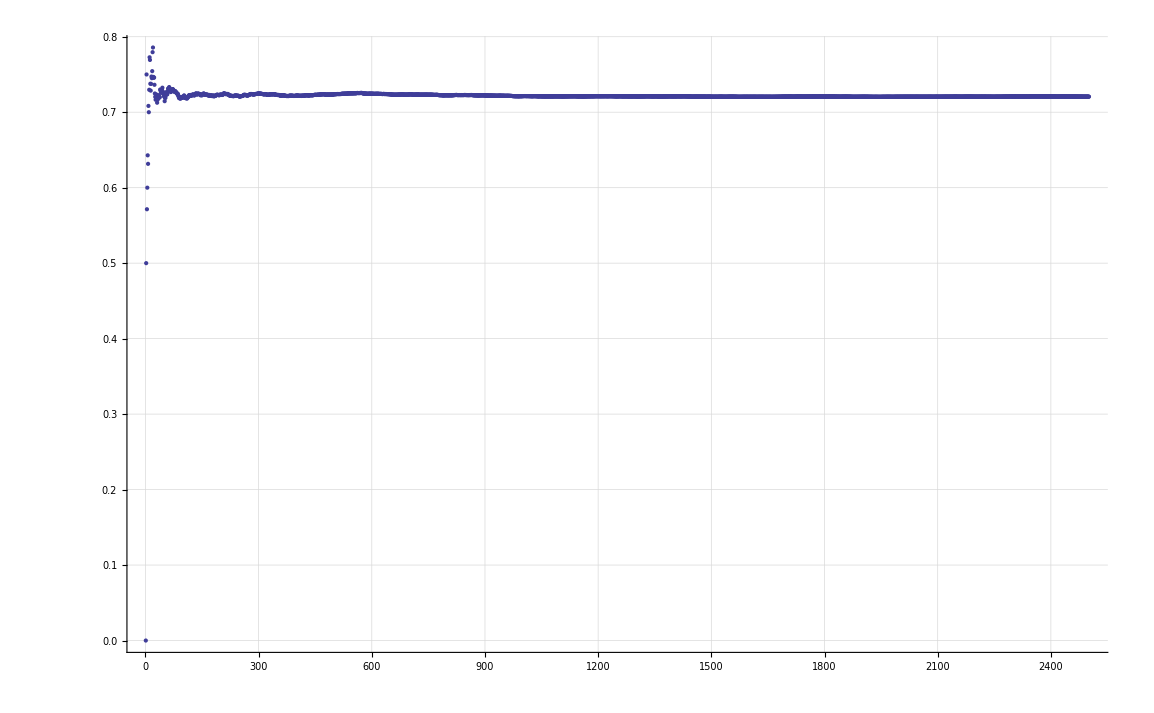

```mathematica
ListPlot[Map[#[[1]]/#[[2]]&,Accumulate[Out[220]]],GridLines->Automatic]
```

```mathematica
With[
{p=5,q=3},
Monitor[
Table[
With[
{t=IntegerDigits[p^max,q]},
{CountCarries[t,p,q],Length[t]}
],
{max,0,(q-1)*q^7}
]
,{max,(q-1)*q^7}
]
]
```

{{1,1},{2,2},{3,3},{5,5},{5,6},{6,8},{6,9},{9,11},{11,12},{8,14},{9,15},{12,17},{13,18},{14,20},{14,21},{16,22},{17,24},{16,25},{19,27},{18,28},{18,30},{22,31},{22,33},{23,34},{28,36},{29,37},{25,39},{34,40},{30,42},{30,43},{29,44},{34,46},{34,47},{35,49},{34,50},{37,52},{33,53},{38,55},{41,56},{43,58},{48,59},{40,61},{44,62},{42,63},{47,65},{50,66},{48,68},{45,69},«4279»,{4292,6339},{4232,6341},{4242,6342},{4273,6344},{4323,6345},{4286,6347},{4277,6348},{4219,6350},{4227,6351},{4222,6353},{4280,6354},{4198,6356},{4189,6357},{4253,6358},{4231,6360},{4283,6361},{4220,6363},{4267,6364},{4255,6366},{4231,6367},{4301,6369},{4306,6370},{4297,6372},{4227,6373},{4196,6375},{4262,6376},{4240,6378},{4262,6379},{4217,6380},{4368,6382},{4263,6383},{4267,6385},{4276,6386},{4260,6388},{4302,6389},{4307,6391},{4222,6392},{4257,6394},{4300,6395},{4277,6397},{4303,6398},{4234,6400},{4258,6401},{4300,6402},{4324,6404},{4260,6405},{4226,6407},{4236,6408}}

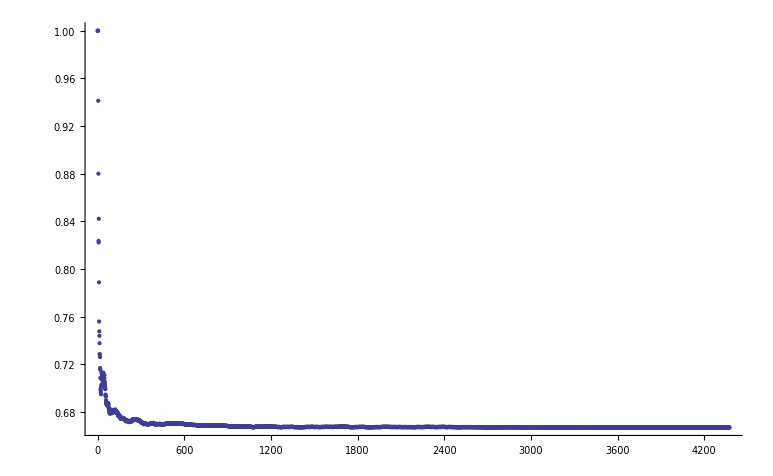

```mathematica
ListPlot[Map[#[[1]]/#[[2]]&,Accumulate[Out[226]]],PlotRange->All]
```

```mathematica
N[Log[3,5]]/2
```

0.732487

```mathematica
N[Log[5,3]]
```

0.682606

```mathematica
IntegerPart[Ceiling[N[Log[3,5000]]]]
```

8

```mathematica
With[
{range=30},
Monitor[
ListPlot3D[
Flatten[
Table[
With[
{max=q^IntegerPart[Ceiling[N[Log[q,5000]]]]},
With[
{t=IntegerDigits[p^max,q]},
{p,q,CountCarries[t,p,q]/Length[t]}
]
]
,{p,Prime[Range[range]]},{q,Select[ Prime[Range[range]],#≠p&]}
],
1]
,PlotLabel->"% of carry ops while calculating p^(x+1) in q-ary notation from p^x"
, ColorFunction->"DarkRainbow"
]
,{p,q}
]
]
```

-Graphics3D-

```mathematica
With[
{range=30},
Monitor[
ListPlot3D[
Flatten[
Table[
With[
{max=q^IntegerPart[Ceiling[N[Log[q,5000]]]]},
With[
{t=IntegerDigits[p^max,q]},
{p,q,CountCarries[t,p,q]/Length[t]}
]
]
,{p,Prime[Range[range]]},{q,Select[ Prime[Range[range+1]],#>p&]}
],
1]
,PlotLabel->"% of transfers while calculating p^(x+1) in q-ary notation from p^x"
, ColorFunction->"DarkRainbow"
]
,{p,q}
]
]
```

-Graphics3D-

```mathematica
With[
{range=40},
Monitor[
ListPlot3D[
Flatten[
Table[
With[
{max=150000},
With[
{t=IntegerDigits[p^max,q]},
{p,q,CountCarries[t,p,q]/Length[t]}
]
]
,{p,Prime[Range[range]]},{q,Select[ Prime[Range[range+1]],#>p&]}
],
1]
,PlotLabel->"% of transfers while calculating p^(x+1) in q-ary notation from p^x"
, ColorFunction->"DarkRainbow",
AxesLabel->{"p","q","ratio"}
]
,{p,q}
]
]
```

-Graphics3D-

```mathematica
IntegerLength[2^50000,3]
```

31547